## NormalVector-example.nb

Example Cellzilla2D notebook.

LGPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.0.α.2 (26-Jun-09)) loaded Sat 27 Jun 2009 14:02:30 using xlr8r 0.74 (13 May 2009)

```mathematica
polygon={{0.6656821861024209,0.5885139068629628},{0.3674265409089722,0.548792012192189},{-0.5083022778120968,0.03200749861905844},{-0.9625187848327785,-0.40634552703524995},{-0.603944818863048,-0.6296344493677282},{-0.2938861906733466,-0.19134629851828722},{0.3771323695082593,0.14124017268253336}};
```

```mathematica
vecs=NormalVector[polygon, #]&/@Range[Length[polygon]]
```

{{0.132015,-0.991248},{0.508225,-0.861224},{0.69443,-0.71956},{0.528603,0.848869},{-0.816372,0.577527},{-0.444089,0.895983},{-0.840309,0.542108}}

```mathematica
midpoints=MidPoint[polygon]
```

{{0.516554,0.568653},{-0.0704379,0.2904},{-0.735411,-0.187169},{-0.783232,-0.51799},{-0.448916,-0.41049},{0.0416231,-0.0250531},{0.521407,0.364877}}

```mathematica
arrows=Arrow/@Transpose[{midpoints, midpoints+vecs}]
```

{Arrow[{{0.516554,0.568653},{0.648569,-0.422595}}],Arrow[{{-0.0704379,0.2904},{0.437787,-0.570825}}],Arrow[{{-0.735411,-0.187169},{-0.0409807,-0.906729}}],Arrow[{{-0.783232,-0.51799},{-0.254629,0.330879}}],Arrow[{{-0.448916,-0.41049},{-1.26529,0.167036}}],Arrow[{{0.0416231,-0.0250531},{-0.402466,0.87093}}],Arrow[{{0.521407,0.364877},{-0.318901,0.906985}}]}

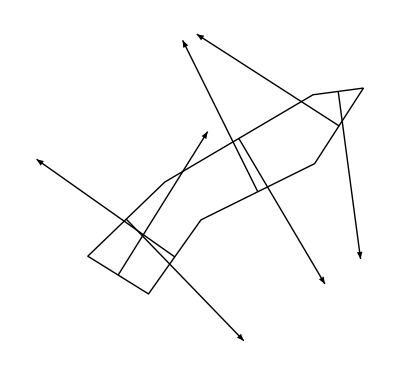

```mathematica
Show[Boundary[polygon], Graphics[arrows]]
```